```mathematica
Clear["Global`*"];
```

```mathematica
"For symmetric α-stable process: E(exp(i U X_t))=exp(-|u|^α)";
ϕ[u_]=Exp[-Abs[u]^α];
```

```mathematica
"Inverse Fourier Transform, assume α in (1,2)";
```

```mathematica
"Plot density of Xt using the Inverse Fourier Transform formula";
```

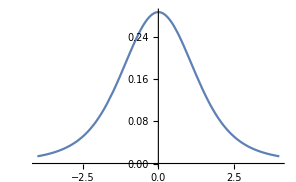

```mathematica
α=3/2;t=1;x=0;Clear[x];Plot[1/(2π)NIntegrate[Exp[-I u x]ϕ[u],{u,-Infinity,Infinity}],{x,-4,4},PlotPoints->20]
```

```mathematica
"Standard Normal cdf";Φ[x_]=1/2(Erf[x/Sqrt[2]]+1);Φc[x_]=1-Φ[x];
```

```mathematica
Plot[Φ[x],{x,-4,4},GridLines->Automatic];
```

```mathematica
"Compute P(M_t>b)=P(τb<=t)=2 P(W_t>b)";F[t_]=Simplify[2Φc[b/Sqrt[t]]]
```

1-Erf[b/(√2 √t)]

```mathematica
"F'[t] is density of τb";
```

```mathematica
f[t_]=F'[t]
```

(b ⅇ^(-b^2/(2 t)))/(√(2 π) t^(3/2))

```mathematica
b=1;Clear[b];Integrate[f[t],{t,0,Infinity}]
```

$Aborted

```mathematica
"ccdf of maximum of B"
```

```mathematica
p[x_,t_]=1/Sqrt[2π t] Exp[-x^2/(2t)]
```

(ⅇ^(-x^2/(2 t)))/(√(2 π) √t)

```mathematica
Simplify[Integrate[p[x,t],{x,-Infinity,Infinity}],t>0]
```

1